```mathematica
ClearAll["Global`*"];
d=0.008*3;(*板厚*)
Lx=0.3;(*m*)
Ly=0.44;(*m*)
Lz=0.2;(*m*)
Vol=Lx*Ly*Lz;(*m^3*)
rho=1000(*kg/m^3*);
(*mass in the experiment*)
massExp=Vol*500;
Print["the volume of the floating body : ",Vol, "m^3"]
Print["mass of the floating body : ",massExp, "kg"]

VolTrue=Lx*Ly*Lz-((Lx-2d)*(Ly-2d)*(Lz-2d));
rhoMaterial=massExp/VolTrue
rhoTypicalPerspex=1.18/1000/((10^-2)^3)(*kg/cm^3*)

Iy=NIntegrate[rhoMaterial*Sqrt[x^2+z^2],{x,-Lx/2,Lx/2},{z,-Lz/2,Lz/2}]-NIntegrate[rhoMaterial*Sqrt[x^2+z^2],{x,-Lx/2+d,Lx/2-d},{z,-Lz/2+d,Lz/2-d}]
Print["Iy = ",Iy]
```

the volume of the floating body : 0.0264m^3

mass of the floating body : 13.2kg

1159.44

1180.

3.23864

Iy = 3.23864

```mathematica
1/12*massExp*(Lx*Lx+Lz*Lz)
```

0.143

```mathematica
Clear["Global`*"]
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"../../../../mathematica_utilities/mathematica_plot_options.nb"}]]

(*name="student@10.0.1.9://home/student/BEM/Kramer2021_0d03/result.json"*)
(*data01DLPF4=Import[FileNameJoin[{ NotebookDirectory[],"Datafile/Numerical_results/LPF4/01D_LPF4.txt"}],"Data"];
data01DFNPF1=Import[FileNameJoin[{ NotebookDirectory[],"Datafile/Numerical_results/FNPF1/01D_FNPF1.txt"}],"Data"];
data01DMeasured1Raw=Import[FileNameJoin[{ NotebookDirectory[],"Datafile/Experimental_results/01D_CI95_Normalized.txt"}],"Data"];
data03DMeasured1Raw=Import[FileNameJoin[{ NotebookDirectory[],"Datafile/Experimental_results/03D_Measured1_Normalized.txt"}],"Data"];
data05DMeasured1Raw=Import[FileNameJoin[{ NotebookDirectory[],"Datafile/Experimental_results/05D_Measured1_Normalized.txt"}],"Data"];
*)

(*ExperimentData=Import[NotebookDirectory[]<>"Ren2015_Fig14_H0d04_T1d2.csv"];
name="/Volumes/home/BEM/流体力学会2023/Ren2015_H0d04_T1d2_potential_2/result.json"*)

ExperimentData=Import[NotebookDirectory[]<>"Ren2015_Fig14_H0d1_T1d2.csv"];
ExperimentData0d04=Import[NotebookDirectory[]<>"Ren2015_Fig14_H0d04_T1d2.csv"];
ExperimentData0d04Heave=Import[NotebookDirectory[]<>"Ren2015_Fig11_H0d04_T1d2_heave.csv"];
ExperimentData0d04Surge=Import[NotebookDirectory[]<>"Ren2015_Fig11_H0d04_T1d2_surge.csv"];
name="/Volumes/home/BEM/20230922流体力学会年会東京農業大学/Ren2015_H0d04_T1d2_potential_2/result.json"
(*name="/Users/tomoaki/BEM/Ren2015_H0d04_T1d2_piston/result.json";*)
name="/Users/tomoaki/BEM/Li_Cheng2018meshB_H0d04_T1d2_piston_positive/result.json"
(*name="/Users/tomoaki/BEM/Li_Cheng2018_H0d04_T1d2_flap_negative/result.json"*)
(*name="/Users/tomoaki/BEM/Li_Cheng2018_H0d04_T1d2_potential/result.json"*)
(*name="/Users/tomoaki/BEM/Li_Cheng2018_H0d04_T1d2_potential_pahse_shift/result.json"*)
(*name="/Users/tomoaki/BEM/Ren2015_H0d04_T1d2_piston_2_positive_start_long/result.json"*)
(*name="/Users/tomoaki/BEM/Ren2015_H0d04_T1d2_piston_2_negative_start_long/result.json"*)
(*name="/Users/tomoaki/BEM/Ren2015_H0d04_T1d2_potential_2/result.json"*)
```

plot2Doption

/Volumes/home/BEM/20230922流体力学会年会東京農業大学/Ren2015_H0d04_T1d2_potential_2/result.json

/Users/tomoaki/BEM/Li_Cheng2018meshB_H0d04_T1d2_piston_positive/result.json

```mathematica
imported=Import[name];
getData[var_,n_:0]:=If[n>0,(var/.imported)[[;;,n]],var/.imported];
importGetData[name_,var_,n_:0]:=With[{imported=Import[name]},If[n>0,(var/.imported)[[;;,n]],var/.imported]];
(*Kramer20210d03=Import[NotebookDirectory[]<>"Kramer2021_0d3.csv"];*)
```

```mathematica
titles=imported[[;;,1]];
Grid[Transpose@{Range[Length[titles]],titles},Background->{{LightGreen,Green}},Frame->All]
```

1 | cpu_time
2 | float_COM
3 | float_EK
4 | float_EP
5 | float_accel
6 | float_area
7 | float_force
8 | float_pitch
9 | float_roll
10 | float_torque
11 | float_velocity
12 | float_yaw
13 | simulation_time
14 | wall_clock_time
15 | water_E
16 | water_EK
17 | water_EP
18 | water_volume

```mathematica
legend=LineLegend[{"Experimental Results (Ren et al., 2015)","Numerical Simulation (BEM)"},LegendMarkerSize->20,LabelStyle->15];
h=0.4;
d=0.1;
H=0.04;
T=1.2;
shift=1.95;
```

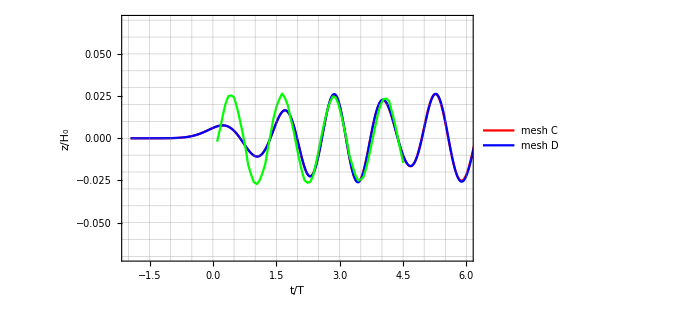

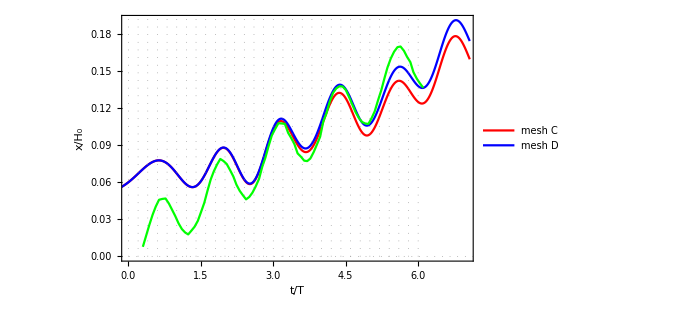

```mathematica
(*メッシュと計算の収束*)
meshC="/Users/tomoaki/BEM/Li_Cheng2018mesh_C_H0d04_T1d2_piston_positive/result.json";
meshD="/Users/tomoaki/BEM/Li_Cheng2018mesh_D_H0d04_T1d2_piston_positive/result.json";

Manipulate[
ListPlot[
{{importGetData[meshC,"float_COM",1]-shift,importGetData[meshC,"float_COM",3]-0.4}ᵀ,
(*{importGetData[meshD,"float_COM",1]-shift,importGetData[meshD,"float_COM",3]-0.4}ᵀ,*)
{#1,#2}&@@@ExperimentData0d04},
PlotRange->{{-0.04,0.04},Automatic},
Joined->{True,True,True},
PlotStyle->{{Red},{Blue},{Green}},
PlotRange->{Automatic,Automatic},
PlotLabel->shift,
FrameLabel->{Style["x",FontSize->20,FontFamily->"Times",Italic],Style["y",FontSize->20,FontFamily->"Times",Italic]},
PlotLegends->Placed[{"mesh C", "mesh D"},{0.65,0.15}],
Evaluate[plot2Doption]
],{shift,3.3882,3.5}]

fig=ListPlot[
{{(importGetData[meshC,"simulation_time"])-shift,(importGetData[meshC,"float_COM",3]-0.4)}ᵀ,
{(importGetData[meshD,"simulation_time"])-shift,(importGetData[meshD,"float_COM",3]-0.4)}ᵀ,
{T*#1+0.1,h#2}&@@@ExperimentData0d04Heave},
Joined->{True,True},
PlotStyle->{{Red},{Blue},{Green}},
PlotRange->{{-2,6.},{-0.07,0.07}},
(*PlotRange->{Automatic,Automatic},*)
GridLines->All(*{Table[i,{i,0.,6.,0.2}],Table[i,{i,-1.,1.,0.5}]}*),
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["z/H_0",FontSize->20,FontFamily->"Times",Italic]},
PlotLegends->Placed[{"mesh C", "mesh D"},{0.65,0.15}],
Evaluate[plot2Doption]
]

ListPlot[
{{importGetData[meshC,"simulation_time"]-shift,(importGetData[meshC,"float_COM",1]-3.3)}ᵀ,
{importGetData[meshD,"simulation_time"]-shift,(importGetData[meshD,"float_COM",1]-3.3)}ᵀ,
{T*#1+0.1,h#2}&@@@ExperimentData0d04Surge},
Joined->{True,True},
PlotStyle->{{Red},{Blue},{Green}},
PlotRange->{{0,7.},Automatic},
(*PlotRange->{Automatic,Automatic},*)
GridLines->{Table[i,{i,0.,6.,0.2}],Table[i,{i,-1.,1.,0.5}]},
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["x/H_0",FontSize->20,FontFamily->"Times",Italic]},
PlotLegends->Placed[{"mesh C", "mesh D"},{0.65,0.15}],
GridLinesStyle->Directive[Gray,Dotted],
PlotLegends->Placed[legend,{0.65,0.15}],
Evaluate[plot2Doption]
]
```

```mathematica
Manipulate[
ListPlot[
{{getData["float_COM",1]-shift,getData["float_COM",3]-0.4}ᵀ
(*,{#1,#2}&@@@ExperimentData,*)
,{#1,#2}&@@@ExperimentData0d04},
PlotRange->All,
Joined->{True,True,False},
PlotStyle->{{Red},{Blue,Dashed}},
PlotRange->{Automatic,Automatic},
PlotLabel->shift,
FrameLabel->{Style["x",FontSize->20,FontFamily->"Times",Italic],Style["y",FontSize->20,FontFamily->"Times",Italic]},
PlotLegends->Placed[legend,{0.65,0.15}],
Evaluate[plot2Doption]
],{shift,3.3882,3.5}]
```

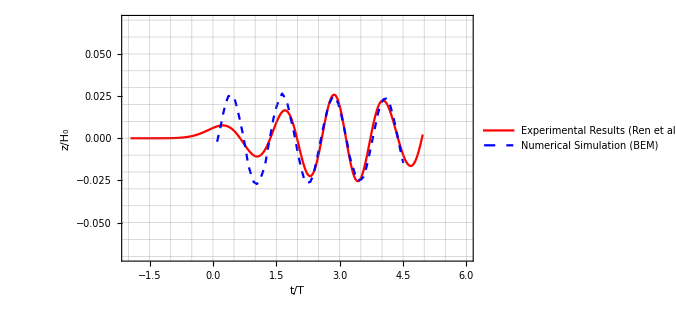

```mathematica
fig=ListPlot[
{{(getData["simulation_time"])-shift,(getData["float_COM",3]-0.4)}ᵀ,
{T*#1+0.1,h#2}&@@@ExperimentData0d04Heave},
Joined->{True,True},
PlotStyle->{{Red},{Blue,Dashed}},
PlotRange->{{-2,6.},{-0.07,0.07}},
(*PlotRange->{Automatic,Automatic},*)
GridLines->All(*{Table[i,{i,0.,6.,0.2}],Table[i,{i,-1.,1.,0.5}]}*),
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["z/H_0",FontSize->20,FontFamily->"Times",Italic]},
PlotLegends->Placed[legend,{0.65,0.15}],
Evaluate[plot2Doption]
]
```

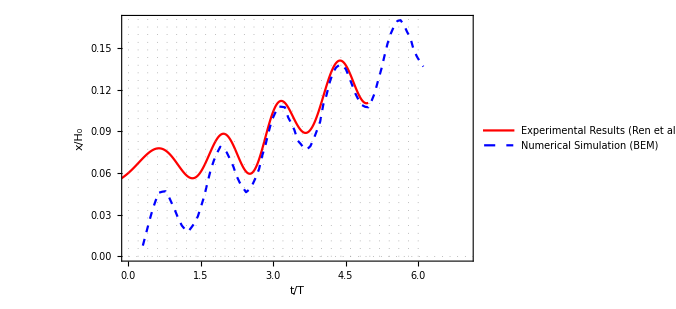

```mathematica
ListPlot[
{{getData["simulation_time"]-shift,(getData["float_COM",1]-3.3)}ᵀ,
{T*#1+0.1,h#2}&@@@ExperimentData0d04Surge},
Joined->{True,True},
PlotStyle->{{Red},{Blue,Dashed}},
PlotRange->{{0,7.},Automatic},
(*PlotRange->{Automatic,Automatic},*)
GridLines->{Table[i,{i,0.,6.,0.2}],Table[i,{i,-1.,1.,0.5}]},
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["x/H_0",FontSize->20,FontFamily->"Times",Italic]},
FrameStyle->Directive[FontSize->20,Black,Thickness[0.002]],GridLines->{Table[i,{i,0.,7.,0.2}],Table[i,{i,-1.,1.,0.5}]},GridLinesStyle->Directive[Gray,Dotted],
PlotLegends->Placed[legend,{0.65,0.15}],
Evaluate[plot2Doption]
]
```

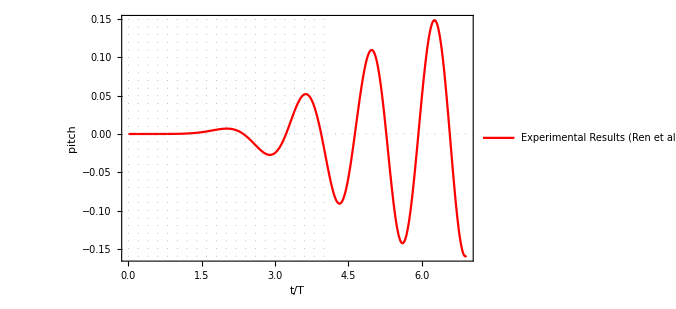

```mathematica
ListPlot[
{getData["simulation_time"],getData["float_pitch"]}ᵀ,
Joined->{True,True},
PlotStyle->{{Red},{Blue,Dashed}},
(*PlotRange->{{0,2.},{-1.,1.}},*)
PlotRange->{Automatic,Automatic},
GridLines->{Table[i,{i,0.,4.,0.2}],Table[i,{i,-1.,1.,0.5}]},
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["pitch",FontSize->20,FontFamily->"Times"]},
FrameStyle->Directive[FontSize->20,Black,Thickness[0.002]],GridLines->{Table[i,{i,0.,4.,0.2}],Table[i,{i,-1.,1.,0.5}]},GridLinesStyle->Directive[Gray,Dotted],
PlotLegends->Placed[legend,{0.65,0.15}],
Evaluate[plot2Doption]
]
```

1/2 (1-Tanh[2.35619-20 π x])

-π

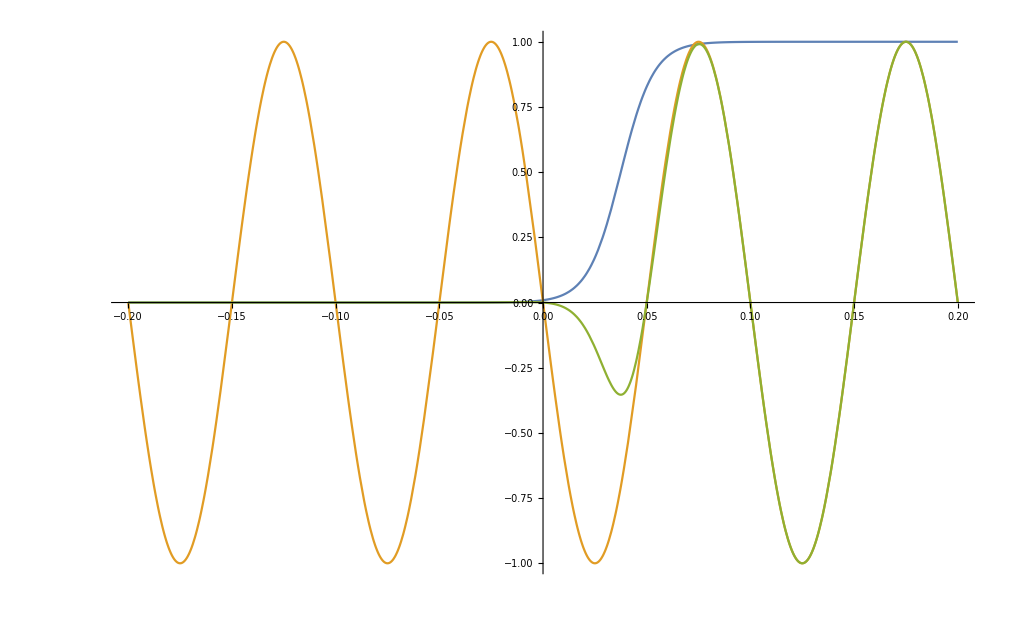

```mathematica
T=1/10;
f[x_]:=((Tanh[2Pi*x/T-0.75Pi]+1)/2);
FullSimplify@f[x]
shift=-Pi
Plot[{f[x],Sin[2Pi*x/T+shift],f[x]*Sin[2Pi*x/T+shift]},{x,-2T,2T}]
```

```mathematica
.00.00
```